# Data Used

Cardano          Market Cap   17.574B
Bitcoin             Market Cap   449.369B
Ethereum       Market Cap  202.995B
Binance           Market Cap   45.805B
Dogecoin        Market Cap	  8.989B
Ripple              Market Cap	  17.636B

NASDAQ 
DowJones 
SP500 
CCi30

# Dates

```mathematica
startdate=DateObject[{2017,11,19}];
enddate=DateObject[{2022,06,19}];
timeperiod={startdate,enddate}; 

(*Defining starting and ending date and the timeperiod for further data analysis in the same time frame*)
```

Defining Names

```mathematica
cryptonames={"Cardano ADA","Bitcoin BTC","Ethereum ETH","Binance BNB","Dogecoin USD","Ripple XRP"};
indexNames={"NASDAQ","DowJones","SP500","CCi30"};

(*Defining  2 lists .first one a list of names of the crypto currencies used and the other list of all indexes used*)
```

# Importing

```mathematica
cardanoADA=Import["C:\\Users\\AmalSebastian\\Desktop\\Final year project\\2.Data Used\\Crypto\\ADA-USD.csv"];
bitcoinBTC=Import["C:\\Users\\AmalSebastian\\Desktop\\Final year project\\2.Data Used\\Crypto\\BTC-USD.csv"];
etheriumETH=Import["C:\\Users\\AmalSebastian\\Desktop\\Final year project\\2.Data Used\\Crypto\\ETH-USD.csv"];
binanceBNB=Import["C:\\Users\\AmalSebastian\\Desktop\\Final year project\\2.Data Used\\Crypto\\BNB-USD.csv"];
dogecoinDOGE=Import["C:\\Users\\AmalSebastian\\Desktop\\Final year project\\2.Data Used\\Crypto\\DOGE-USD.csv"];
rippleXRP=Import["C:\\Users\\AmalSebastian\\Desktop\\Final year project\\2.Data Used\\Crypto\\XRP-USD.csv"];
```

```mathematica
NASDAQ=Import["C:\\Users\\AmalSebastian\\Desktop\\Final year project\\2.Data Used\\Index\\^IXIC.csv"];
dowJones=Import["C:\\Users\\AmalSebastian\\Desktop\\Final year project\\2.Data Used\\Index\\dowJones.csv"];
sp500=Import["C:\\Users\\AmalSebastian\\Desktop\\Final year project\\2.Data Used\\Index\\sp500.csv"];
cci30=Import["C:\\Users\\AmalSebastian\\Desktop\\Final year project\\2.Data Used\\Index\\cci30.csv"];


(*Importing data from local storage*)
```

# Cleaning

```mathematica
(*After checking the dimension(//Dimension) and Table form(//TableForm) of data it is evident that the uploaded  data have many excess columns so, we are defining a function (from class lecture) used to clean data and select just the columns with "date" and with "closing" price*)

deleteColumn[m_,cols_Integer] :=Delete[Transpose[m],cols]//Transpose;
deleteColumn[m_,cols_List] :=Delete[Transpose[m],Map[{#}&,cols]]//Transpose;
insertColumn[m_,newCol_,pos_]:=Insert[Transpose[m],newCol,pos]//Transpose;
```

```mathematica
cardanoclean=deleteColumn[cardanoADA,{2,3,4,6,7}];
bitcoinclean=deleteColumn[bitcoinBTC,{2,3,4,6,7}];
etheriumclean=deleteColumn[etheriumETH,{2,3,4,6,7}];
binanceclean=deleteColumn[binanceBNB,{2,3,4,6,7}];
dogecoinclean=deleteColumn[dogecoinDOGE,{2,3,4,6,7}];
rippleclean=deleteColumn[rippleXRP,{2,3,4,6,7}];
```

```mathematica
sp500clean=deleteColumn[sp500,{2,3,4,6,7}];
NASDAQclean=deleteColumn[NASDAQ,{2,3,4,6,7}];
dowJonesclean=deleteColumn[dowJones,{2,3,4,6,7}];
cci30clean=deleteColumn[cci30,{2,3,4,6}];
```

# Timeseries

```mathematica
TScardano=TimeSeries[cardanoclean[[2;;]]];
TSbitcoin=TimeSeries[bitcoinclean[[2;;]]];
TSetherium=TimeSeries[etheriumclean[[2;;]]];
TSbinance=TimeSeries[binanceclean[[2;;]]];
TSdogecoin=TimeSeries[dogecoinclean[[2;;]]];
TSripple=TimeSeries[rippleclean[[2;;]]];
```

```mathematica
TSsp500=TimeSeries[sp500clean[[2;;]]];
TSNASDAQ=TimeSeries[NASDAQclean[[2;;]]];
TSdowJones=TimeSeries[dowJonesclean[[2;;]]];
TScci30=TimeSeries[cci30clean[[2;;]]];
(*Selecting just the data and removing the headings
(or the heading strings "Date"-"Closing" as they are not numeric values for the timeseries creation)
 of the column.Then creating a timeseries of this data*)
```

```mathematica
cryptoTslist={TScardano,TSbitcoin,TSetherium,TSbinance,TSdogecoin,TSripple};
indexTslist={TSNASDAQ,TSdowJones,TSsp500};
allindexTSlist={TSNASDAQ,TSdowJones,TSsp500,TScci30};
(*Creating 3 lists of timeseris*)
```

# Plotting Data

Defining and Plotting all data as Histogram and DatelistPlot

```mathematica
(*Using datelistplot function to plot all data and then using histogram plots as well to see if there and any trends or how the distribution of values are*)
plotDJ=DateListPlot[TSdowJones,
FrameLabel->{{HoldForm[USD],None},{HoldForm[YEAR],None}},
PlotLabel->HoldForm[Dow Jones Data from 2017],
LabelStyle->{FontFamily->"Alef",GrayLevel[0],Italic},Joined->True,Filling->Bottom];
plotsp500=DateListPlot[TSsp500,
FrameLabel->{{HoldForm[USD],None},{HoldForm[YEAR],None}},
PlotLabel->HoldForm[S& P 500 Data from 2017],
LabelStyle->{FontFamily->"Alef",GrayLevel[0],Italic},Joined->True,Filling->Bottom];
plotcci30=DateListPlot[TScci30,
FrameLabel->{{HoldForm[USD],None},{HoldForm[YEAR],None}},
PlotLabel->HoldForm[cci30 Crypto Index],
LabelStyle->{FontFamily->"Alef",GrayLevel[0],Italic},Joined->True,Filling->Bottom];
plotNASDAQ=DateListPlot[TSNASDAQ,
FrameLabel->{{HoldForm[USD],None},{HoldForm[YEAR],None}},
PlotLabel->HoldForm[NASDAQ Data from 2017],
LabelStyle->{FontFamily->"Alef",GrayLevel[0],Italic},Joined->True,Filling->Bottom];
```

Histogram plot of Indexes

```mathematica
histDOW=Histogram[
Flatten[TSdowJones],40,
AxesLabel->{HoldForm[Value],HoldForm[Frequency]},
LabelStyle->{GrayLevel[0],Italic},
PlotLabel->HoldForm[Dow Jones],
LabelStyle->{GrayLevel[0],Bold},ChartElementFunction->"GradientScaleRectangle",LabelingFunction->Above];
histSP=Histogram[
Flatten[TSsp500],40,
AxesLabel->{HoldForm[Value],HoldForm[Frequency]},
LabelStyle->{GrayLevel[0],Italic},
PlotLabel->HoldForm[S& P 500],
LabelStyle->{GrayLevel[0],Bold},ChartElementFunction->"GradientScaleRectangle",LabelingFunction->Above];
histCCi=Histogram[
Flatten[TScci30],40,
AxesLabel->{HoldForm[Value],HoldForm[Frequency]},
LabelStyle->{GrayLevel[0],Italic},
PlotLabel->HoldForm[cci30],
LabelStyle->{GrayLevel[0],Bold},ChartElementFunction->"GradientScaleRectangle",LabelingFunction->Above];
histNAS=Histogram[
Flatten[TSNASDAQ],40,
AxesLabel->{HoldForm[Value],HoldForm[Frequency]},
LabelStyle->{GrayLevel[0],Italic},
PlotLabel->HoldForm[Nasdaq],
LabelStyle->{GrayLevel[0],Bold},ChartElementFunction->"GradientScaleRectangle",LabelingFunction->Above];
```

DateListPlot of Crypto as first visualisation

```mathematica
a=DateListPlot[TScardano,
FrameLabel->{{HoldForm[USD],None},{HoldForm[YEAR],None}},
PlotLabel->HoldForm[cardano Crypto ],
LabelStyle->{FontFamily->"Alef",GrayLevel[0]},Joined->True,Filling->Bottom];
b=DateListPlot[TSbinance,
FrameLabel->{{HoldForm[USD],None},{HoldForm[YEAR],None}},
PlotLabel->HoldForm[binance Coin Crypto ],
LabelStyle->{FontFamily->"Alef",GrayLevel[0]},Joined->True,Filling->Bottom];
c=DateListPlot[TSbitcoin,
FrameLabel->{{HoldForm[USD],None},{HoldForm[YEAR],None}},
PlotLabel->HoldForm[bitcoin Crypto ],
LabelStyle->{FontFamily->"Alef",GrayLevel[0]},Joined->True,Filling->Bottom];
d=DateListPlot[TSdogecoin,
FrameLabel->{{HoldForm[USD],None},{HoldForm[YEAR],None}},
PlotLabel->HoldForm[dogecoin Crypto ],
LabelStyle->{FontFamily->"Alef",GrayLevel[0]},PlotRange->{0,0.75},Joined->True,Filling->Bottom];
e=DateListPlot[TSetherium,
FrameLabel->{{HoldForm[USD],None},{HoldForm[YEAR],None}},
PlotLabel->HoldForm[ethereum Crypto ],
LabelStyle->{FontFamily->"Alef",GrayLevel[0]},Joined->True,Filling->Bottom];               
f=DateListPlot[TSripple,
FrameLabel->{{HoldForm[USD],None},{HoldForm[YEAR],None}},
PlotLabel->HoldForm[ripple Crypto ],
LabelStyle->{FontFamily->"Alef",GrayLevel[0]},PlotRange->{0,3.7},Joined->True,Filling->Bottom];
```

Histogram of Crypto Currency

```mathematica
histCar=Histogram[Flatten[TScardano],40,
AxesLabel->{HoldForm[Value],HoldForm[Frequency]},
LabelStyle->{GrayLevel[0],Italic},
PlotLabel->HoldForm[Cardano],LabelStyle->{GrayLevel[0],Bold},ChartElementFunction->"GradientScaleRectangle",LabelingFunction->Above];
histBit=Histogram[Flatten[TSbitcoin],40,
AxesLabel->{HoldForm[Value],HoldForm[Frequency]},
LabelStyle->{GrayLevel[0],Italic},
PlotLabel->HoldForm[Bitcoin],LabelStyle->{GrayLevel[0],Bold},ChartElementFunction->"GradientScaleRectangle",LabelingFunction->Above];
histEth=Histogram[Flatten[TSetherium],40,
AxesLabel->{HoldForm[Value],HoldForm[Frequency]},
LabelStyle->{GrayLevel[0],Italic},
PlotLabel->HoldForm[Etherium],LabelStyle->{GrayLevel[0],Bold},ChartElementFunction->"GradientScaleRectangle",LabelingFunction->Above];
histBin=Histogram[Flatten[TSbinance],40,
AxesLabel->{HoldForm[Value],HoldForm[Frequency]},
LabelStyle->{GrayLevel[0],Italic},
PlotLabel->HoldForm[Binance],LabelStyle->{GrayLevel[0],Bold},ChartElementFunction->"GradientScaleRectangle",LabelingFunction->Above];
histDog=Histogram[Flatten[TSdogecoin],40,
AxesLabel->{HoldForm[Value],HoldForm[Frequency]},
LabelStyle->{GrayLevel[0],Italic},
PlotLabel->HoldForm[Dogecoin],LabelStyle->{GrayLevel[0],Bold},ChartElementFunction->"GradientScaleRectangle",LabelingFunction->Above];
histripp=Histogram[Flatten[TSripple],40,
AxesLabel->{HoldForm[Value],HoldForm[Frequency]},
LabelStyle->{GrayLevel[0],Italic},
PlotLabel->HoldForm[Ripple],LabelStyle->{GrayLevel[0],Bold},ChartElementFunction->"GradientScaleRectangle",LabelingFunction->Above];
```

```mathematica
(*Plotting both indexes and cryptocurrencies *)
```

Plotting results

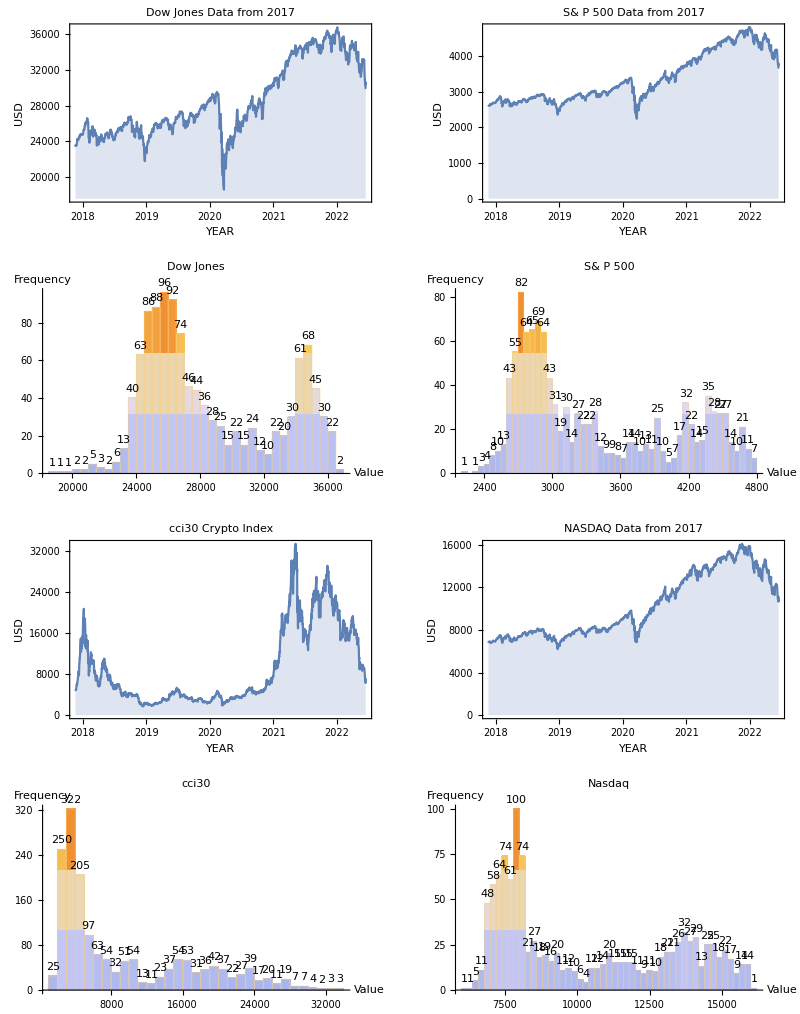

```mathematica
(*Using graphics grid plot to combine all line plots for index and their histogram*)

GraphicsGrid[
{{plotDJ,plotsp500},{histDOW,histSP},{plotcci30,plotNASDAQ},{histCCi,histNAS}},
ImageSize->Full,
LabelStyle->{FontFamily->"Alef",GrayLevel[0]}]
```

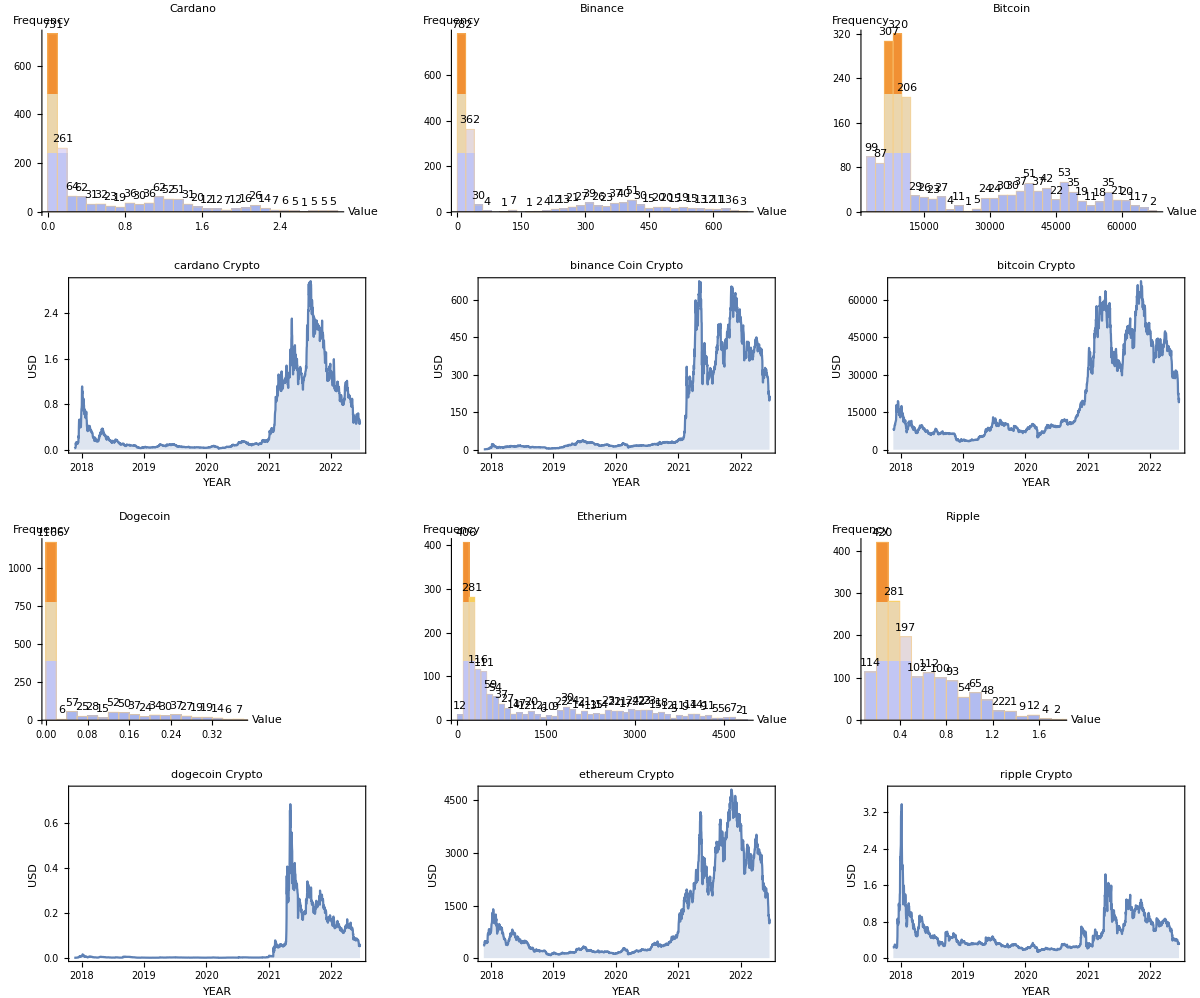

```mathematica
(*Using graphics grid plot to combine all line plots for crypto and their histogram*)
GraphicsGrid[
{{histCar,histBin,histBit},{a,b,c} ,{histDog,histEth ,histripp},{d,e,f}},
ImageSize->Full,
LabelStyle->{FontFamily->"Alef",GrayLevel[0]}]

cryptoTslist={TScardano,TSbitcoin,TSetherium,TSbinance,TSdogecoin,TSripple};
indexTslist={TScci30,TSsp500,TSNASDAQ,TSdowJones};
(*Using Graphicsgrid formatting the plot and plotting all data that *)
```

# Price Correlation

```mathematica
businessdate=TimeSeriesResample[#, "BusinessDay"]["Dates"] & /@ indexTslist;
BDcryptoTslist=TimeSeriesResample[#, "BusinessDay"]["Values"] &/@ cryptoTslist ;
BDindexTslist=TimeSeriesResample[#, "BusinessDay"]["Values"] &/@ allindexTSlist;

(*In 'businessdate' variable we fetch the business day date from the Index data then Extracting only Business day data for analysis "BDcryptoTslist","BDindexTslist" to justify all time series data of various asset classes on the same length*)

times=businessdate[[1,2;;]];
(*Define a variable for business day dates*)
```

```mathematica
allTSlist=
{BDcryptoTslist[[1]],BDcryptoTslist[[2]],BDcryptoTslist[[3]],BDcryptoTslist[[4]],
BDcryptoTslist[[5]],BDcryptoTslist[[6]],BDindexTslist[[1]],BDindexTslist[[2]],
BDindexTslist[[3]],BDindexTslist[[4]]};

allTSlist//Dimensions

(*Grouping all timeseries and checking for the dimension ,as dimensions has to be equal for further doing correlation*)
```

{10,1148}

```mathematica
allCorrelation = Correlation[Transpose@allTSlist]; (*Finding the correlation of the matrix*)

alldataNames={"Cardano ADA","Bitcoin BTC","Ethereum ETH",
"Binance BNB","Dogecoin USD","Ripple XRP","NASDAQ",
"DowJones","SP500","CCi30"};

(*Calculating the correlation of prices for all data and then defining a list with all names of data to attach to the correaltion matics*)
```

```mathematica
allCorrelation//TableForm  (*Checking the correlation matics before plotting *)
```

1. | 0.886938 | 0.92166 | 0.892458 | 0.879699 | 0.705429 | 0.807687 | 0.831921 | 0.826866 | 0.934565
0.886938 | 1. | 0.926565 | 0.923006 | 0.79264 | 0.575206 | 0.903863 | 0.903449 | 0.909861 | 0.930877
0.92166 | 0.926565 | 1. | 0.964168 | 0.855998 | 0.657632 | 0.854848 | 0.887557 | 0.899235 | 0.936029
0.892458 | 0.923006 | 0.964168 | 1. | 0.883026 | 0.599369 | 0.851578 | 0.897066 | 0.902288 | 0.910587
0.879699 | 0.79264 | 0.855998 | 0.883026 | 1. | 0.622755 | 0.749138 | 0.793523 | 0.778914 | 0.861966
0.705429 | 0.575206 | 0.657632 | 0.599369 | 0.622755 | 1. | 0.3876 | 0.46376 | 0.429794 | 0.797982
0.807687 | 0.903863 | 0.854848 | 0.851578 | 0.749138 | 0.3876 | 1. | 0.945944 | 0.978075 | 0.790504
0.831921 | 0.903449 | 0.887557 | 0.897066 | 0.793523 | 0.46376 | 0.945944 | 1. | 0.985453 | 0.81929
0.826866 | 0.909861 | 0.899235 | 0.902288 | 0.778914 | 0.429794 | 0.978075 | 0.985453 | 1. | 0.810556
0.934565 | 0.930877 | 0.936029 | 0.910587 | 0.861966 | 0.797982 | 0.790504 | 0.81929 | 0.810556 | 1.

```mathematica
(*Plotting the whole correlation matrix in a more graphical appealing form,with all relavent names associated to the columns and rows*)
pcorrelationmatrix=Map[
If[# ≠ 1,
Item[NumberForm[#,2],
Background->ColorData["LightTemperatureMap"][Rescale[#,{0,1}]]],
 Item["", Background->Gray]]&,allCorrelation,{2}];

pcorrelationmatrix=Prepend[pcorrelationmatrix,alldataNames];
pcorrelationmatrix=Join[List/@Prepend[alldataNames,""],pcorrelationmatrix,2];

Grid[pcorrelationmatrix,
 Dividers-> All,
 Spacings->{2, 1.5},
 Background->White
 ]
```

| Cardano ADA | Bitcoin BTC | Ethereum ETH | Binance BNB | Dogecoin USD | Ripple XRP | NASDAQ | DowJones | SP500 | CCi30
Cardano ADA |  | 0.89 | 0.92 | 0.89 | 0.88 | 0.71 | 0.81 | 0.83 | 0.83 | 0.93
Bitcoin BTC | 0.89 |  | 0.93 | 0.92 | 0.79 | 0.58 | 0.9 | 0.9 | 0.91 | 0.93
Ethereum ETH | 0.92 | 0.93 |  | 0.96 | 0.86 | 0.66 | 0.85 | 0.89 | 0.9 | 0.94
Binance BNB | 0.89 | 0.92 | 0.96 |  | 0.88 | 0.6 | 0.85 | 0.9 | 0.9 | 0.91
Dogecoin USD | 0.88 | 0.79 | 0.86 | 0.88 |  | 0.62 | 0.75 | 0.79 | 0.78 | 0.86
Ripple XRP | 0.71 | 0.58 | 0.66 | 0.6 | 0.62 |  | 0.39 | 0.46 | 0.43 | 0.8
NASDAQ | 0.81 | 0.9 | 0.85 | 0.85 | 0.75 | 0.39 |  | 0.95 | 0.98 | 0.79
DowJones | 0.83 | 0.9 | 0.89 | 0.9 | 0.79 | 0.46 | 0.95 |  | 0.99 | 0.82
SP500 | 0.83 | 0.91 | 0.9 | 0.9 | 0.78 | 0.43 | 0.98 | 0.99 |  | 0.81
CCi30 | 0.93 | 0.93 | 0.94 | 0.91 | 0.86 | 0.8 | 0.79 | 0.82 | 0.81 |

# Returns Correlation

```mathematica
(*Calculating the Log and then finding the difference of the value to find the returns of each asset*)
cardanoReturns=Differences[Log[allTSlist[[1]]]];
bitcoinReturns=Differences[Log[allTSlist[[2]]]];
etheriumReturns=Differences[Log[allTSlist[[3]]]];
binanceReturns=Differences[Log[allTSlist[[4]]]];
dogecoinReturns=Differences[Log[allTSlist[[5]]]];
rippleReturns=Differences[Log[allTSlist[[6]]]];

NASDAQReturns=Differences[Log[allTSlist[[7]]]];
dowJonesReturns=Differences[Log[allTSlist[[8]]]];
sp500Returns=Differences[Log[allTSlist[[9]]]];
cci30Returns=Differences[Log[allTSlist[[10]]]];
```

```mathematica
(*Creating a timeseries for this log returns*)
cardanoReturnsTS=TimeSeries[cardanoReturns,{times}];
bitcoinReturnsTS=TimeSeries[bitcoinReturns,{times}];
etheriumReturnsTS=TimeSeries[etheriumReturns,{times}];
binanceReturnsTS=TimeSeries[binanceReturns,{times}];
dogecoinReturnsTS=TimeSeries[dogecoinReturns,{times}];
rippleReturnsTS=TimeSeries[rippleReturns,{times}];
sp500ReturnsTS=TimeSeries[sp500Returns,{times}];
NASDAQReturnsTS=TimeSeries[NASDAQReturns,{times}];
dowJonesReturnsTS=TimeSeries[dowJonesReturns,{times}];
cci30ReturnsTS=TimeSeries[cci30Returns,{times}];
```

```mathematica
allTSReturns={cardanoReturnsTS,bitcoinReturnsTS,etheriumReturnsTS,binanceReturnsTS,dogecoinReturnsTS,rippleReturnsTS,NASDAQReturnsTS,dowJonesReturnsTS,sp500ReturnsTS,cci30ReturnsTS};
logReturnsData = TimeSeriesResample[#]["Values"] &/@ allTSReturns;
```

```mathematica
(*Repeating the Correlation but on the log returns value and then plotting it graphically *)
logreturnCorrelation = Correlation[Transpose@logReturnsData];
rcorrelationmatrix=Map[
If[# ≠ 1,
Item[NumberForm[#,2],
Background->ColorData["LightTemperatureMap"][Rescale[#,{0,1}]]],
 Item["1", Background->Gray]]&,logreturnCorrelation,{2}];

rcorrelationmatrix=Prepend[rcorrelationmatrix,alldataNames];
rcorrelationmatrix=Join[List/@Prepend[alldataNames,""],rcorrelationmatrix,2];

Grid[rcorrelationmatrix, 
Dividers-> All,
 Spacings->{2, 1.5},
 Background->White]
```

| Cardano ADA | Bitcoin BTC | Ethereum ETH | Binance BNB | Dogecoin USD | Ripple XRP | NASDAQ | DowJones | SP500 | CCi30
Cardano ADA | 1 | 0.62 | 0.67 | 0.53 | 0.47 | 0.63 | 0.24 | 0.21 | 0.23 | 0.78
Bitcoin BTC | 0.62 | 1 | 0.77 | 0.64 | 0.5 | 0.53 | 0.27 | 0.23 | 0.26 | 0.88
Ethereum ETH | 0.67 | 0.77 | 1 | 0.63 | 0.5 | 0.61 | 0.3 | 0.27 | 0.29 | 0.89
Binance BNB | 0.53 | 0.64 | 0.63 | 1 | 0.47 | 0.48 | 0.24 | 0.23 | 0.24 | 0.72
Dogecoin USD | 0.47 | 0.5 | 0.5 | 0.47 | 1 | 0.42 | 0.16 | 0.15 | 0.16 | 0.58
Ripple XRP | 0.63 | 0.53 | 0.61 | 0.48 | 0.42 | 1 | 0.21 | 0.19 | 0.2 | 0.74
NASDAQ | 0.24 | 0.27 | 0.3 | 0.24 | 0.16 | 0.21 | 1 | 0.85 | 0.94 | 0.3
DowJones | 0.21 | 0.23 | 0.27 | 0.23 | 0.15 | 0.19 | 0.85 | 1 | 0.97 | 0.27
SP500 | 0.23 | 0.26 | 0.29 | 0.24 | 0.16 | 0.2 | 0.94 | 0.97 | 1 | 0.3
CCi30 | 0.78 | 0.88 | 0.89 | 0.72 | 0.58 | 0.74 | 0.3 | 0.27 | 0.3 | 1

# Volatility

```mathematica
(*Calculating the standard deviation in a week for all data *)
cardanoVolaTS=MovingMap[StandardDeviation,cardanoReturnsTS,Quantity[1,"Weeks"]];
bitcoinVolaTS=MovingMap[StandardDeviation,bitcoinReturnsTS,Quantity[1,"Weeks"]];
etheriumVolaTS=MovingMap[StandardDeviation,etheriumReturnsTS,Quantity[1,"Weeks"]];
binanceVolaTS=MovingMap[StandardDeviation,binanceReturnsTS,Quantity[1,"Weeks"]];
dogecoinVolaTS=MovingMap[StandardDeviation,dogecoinReturnsTS,Quantity[1,"Weeks"]];
rippleVolaTS=MovingMap[StandardDeviation,rippleReturnsTS,Quantity[1,"Weeks"]];
sp500VolaTS=MovingMap[StandardDeviation,sp500ReturnsTS,Quantity[1,"Weeks"]];
NASDAQVolaTS=MovingMap[StandardDeviation,NASDAQReturnsTS,Quantity[1,"Weeks"]];
dowJonesVolaTS=MovingMap[StandardDeviation,dowJonesReturnsTS,Quantity[1,"Weeks"]];
cci30VolaTS=MovingMap[StandardDeviation,cci30ReturnsTS,Quantity[1,"Weeks"]];
```

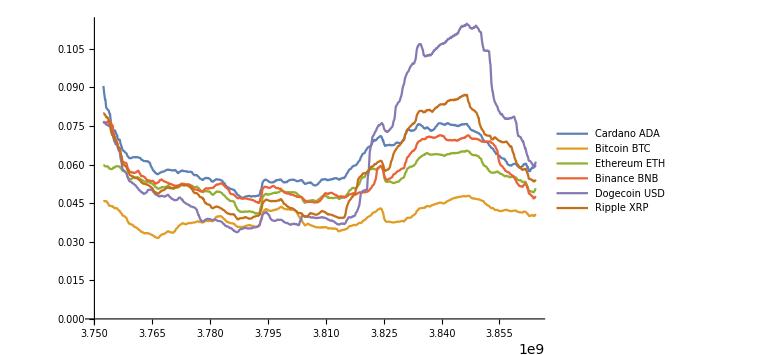

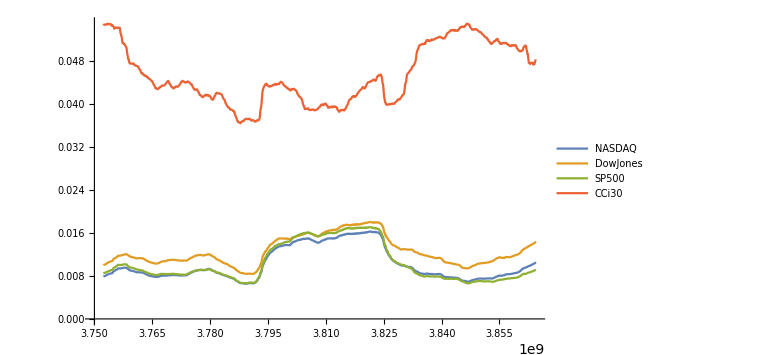

```mathematica
(*Plotting the list line plot of the moving average of volatility of all crypto in one graph and all index in another so we can initially identify how volatile they are and the trend*)

l1=ListLinePlot[
{MovingAverage[cardanoVolaTS,"Year"],MovingAverage[bitcoinVolaTS,"Year"],
MovingAverage[etheriumVolaTS,"Year"],MovingAverage[binanceVolaTS,"Year"],
MovingAverage[dogecoinVolaTS,"Year"],MovingAverage[rippleVolaTS,"Year"]},
PlotRange->All,
ImageSize->Large,
PlotLegends->(
lgd={"Cardano ADA","Bitcoin BTC","Ethereum ETH","Binance BNB","Dogecoin USD","Ripple XRP"})]

l3=ListLinePlot[{
MovingAverage[sp500VolaTS,"Year"],MovingAverage[NASDAQVolaTS,"Year"],
MovingAverage[dowJonesVolaTS,"Year"],MovingAverage[cci30VolaTS,"Year"]},
PlotRange->All,
ImageSize->Large,
PlotLegends->(
lgd={"NASDAQ","DowJones","SP500","CCi30"})]
```

Plotting the volatility Histogram to see the range of Volatility and the frequency

```mathematica
volatDOW=Histogram[
Flatten[dowJonesVolaTS],40,
AxesLabel->{HoldForm[Value],HoldForm[Frequency]},LabelStyle->{GrayLevel[0],Italic},PlotLabel->HoldForm[Dow Jones],LabelStyle->{GrayLevel[0],Bold}];
volatSP=Histogram[
Flatten[sp500VolaTS],40,
AxesLabel->{HoldForm[Value],HoldForm[Frequency]},LabelStyle->{GrayLevel[0],Italic},PlotLabel->HoldForm[S& P 500],LabelStyle->{GrayLevel[0],Bold}];
volatCCi=Histogram[
Flatten[cci30VolaTS],40,
AxesLabel->{HoldForm[Value],HoldForm[Frequency]},LabelStyle->{GrayLevel[0],Italic},PlotLabel->HoldForm[cci30],LabelStyle->{GrayLevel[0],Bold}];
volatNAS=Histogram[
Flatten[NASDAQVolaTS],40,
AxesLabel->{HoldForm[Value],HoldForm[Frequency]},LabelStyle->{GrayLevel[0],Italic},PlotLabel->HoldForm[Nasdaq],LabelStyle->{GrayLevel[0],Bold}];
volatCar=Histogram[Flatten[cardanoVolaTS],40,
AxesLabel->{HoldForm[Value],HoldForm[Frequency]},LabelStyle->{GrayLevel[0],Italic},PlotLabel->HoldForm[Cardano],LabelStyle->{GrayLevel[0],Bold}];
volatBit=Histogram[Flatten[bitcoinVolaTS],40,
AxesLabel->{HoldForm[Value],HoldForm[Frequency]},LabelStyle->{GrayLevel[0],Italic},PlotLabel->HoldForm[Bitcoin],LabelStyle->{GrayLevel[0],Bold}];
volatEth=Histogram[Flatten[etheriumVolaTS],40,
AxesLabel->{HoldForm[Value],HoldForm[Frequency]},LabelStyle->{GrayLevel[0],Italic},PlotLabel->HoldForm[Etherium],LabelStyle->{GrayLevel[0],Bold}];
volatBin=Histogram[Flatten[binanceVolaTS],40,
AxesLabel->{HoldForm[Value],HoldForm[Frequency]},LabelStyle->{GrayLevel[0],Italic},PlotLabel->HoldForm[Binance],LabelStyle->{GrayLevel[0],Bold}];
volatDog=Histogram[Flatten[dogecoinVolaTS],40,
AxesLabel->{HoldForm[Value],HoldForm[Frequency]},LabelStyle->{GrayLevel[0],Italic},PlotLabel->HoldForm[Dogecoin],LabelStyle->{GrayLevel[0],Bold}];
volatripp=Histogram[Flatten[rippleVolaTS],40,
AxesLabel->{HoldForm[Value],HoldForm[Frequency]},LabelStyle->{GrayLevel[0],Italic},PlotLabel->HoldForm[Ripple],LabelStyle->{GrayLevel[0],Bold}];
```

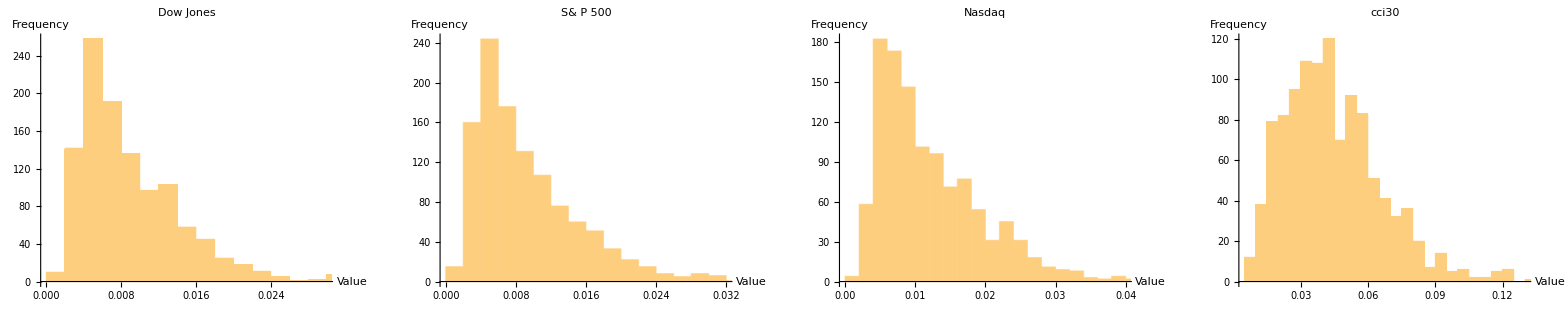

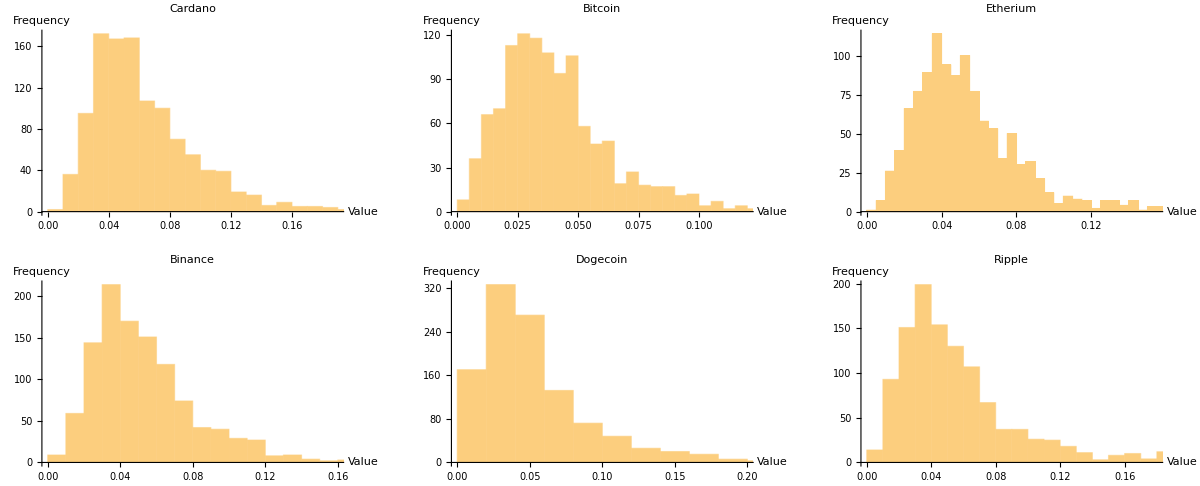

```mathematica
(*Plotting both graphs as a histogram to see the frequency and value of the change*)
GraphicsGrid[
{{volatDOW,volatSP,volatNAS,volatCCi}},
ImageSize->Full,
LabelStyle->{FontFamily->"Alef",GrayLevel[0]}]    
GraphicsGrid[
{{volatCar,volatBit,volatEth},{volatBin,volatDog,volatripp}},
ImageSize->Full,
LabelStyle->{FontFamily->"Alef",GrayLevel[0]}]
```

```mathematica
stdallTS=
{cardanoVolaTS,bitcoinVolaTS,etheriumVolaTS,binanceVolaTS,dogecoinVolaTS,rippleVolaTS,NASDAQVolaTS,dowJonesVolaTS,sp500VolaTS,cci30VolaTS};

(*Grouping all timesereis of volatility into a list and creating a correlation matrix for that*)
```

```mathematica
stdData = TimeSeriesResample[#]["Values"] &/@ stdallTS;
stdCorrelation = Correlation[Transpose@stdData];

stdcorrelationmatrix=Map[
If[# ≠ 1,
Item[NumberForm[#,2],
Background->ColorData["LightTemperatureMap"][Rescale[#,{0,1}]]],
 Item["1", Background->Gray]]&,stdCorrelation,{2}];

(*Adding the names to respective columns of data correlation table*)
stdcorrelationmatrix=Prepend[stdcorrelationmatrix,alldataNames];
stdcorrelationmatrix=Join[List/@Prepend[alldataNames,"Correlation"],stdcorrelationmatrix,2];
```

```mathematica
Grid[
stdcorrelationmatrix,
 Dividers-> All,
 Spacings->{2, 1.5},
 Background->White
]
```

Correlation | Cardano ADA | Bitcoin BTC | Ethereum ETH | Binance BNB | Dogecoin USD | Ripple XRP | NASDAQ | DowJones | SP500 | CCi30
Cardano ADA | 1 | 0.56 | 0.62 | 0.55 | 0.44 | 0.64 | 0.098 | 0.093 | 0.1 | 0.63
Bitcoin BTC | 0.56 | 1 | 0.77 | 0.6 | 0.43 | 0.53 | 0.26 | 0.28 | 0.29 | 0.83
Ethereum ETH | 0.62 | 0.77 | 1 | 0.61 | 0.45 | 0.63 | 0.28 | 0.3 | 0.31 | 0.89
Binance BNB | 0.55 | 0.6 | 0.61 | 1 | 0.49 | 0.61 | 0.12 | 0.13 | 0.14 | 0.7
Dogecoin USD | 0.44 | 0.43 | 0.45 | 0.49 | 1 | 0.55 | -0.012 | -0.022 | -0.0069 | 0.47
Ripple XRP | 0.64 | 0.53 | 0.63 | 0.61 | 0.55 | 1 | -0.0089 | 0.018 | 0.017 | 0.67
NASDAQ | 0.098 | 0.26 | 0.28 | 0.12 | -0.012 | -0.0089 | 1 | 0.9 | 0.96 | 0.27
DowJones | 0.093 | 0.28 | 0.3 | 0.13 | -0.022 | 0.018 | 0.9 | 1 | 0.98 | 0.27
SP500 | 0.1 | 0.29 | 0.31 | 0.14 | -0.0069 | 0.017 | 0.96 | 0.98 | 1 | 0.28
CCi30 | 0.63 | 0.83 | 0.89 | 0.7 | 0.47 | 0.67 | 0.27 | 0.27 | 0.28 | 1

# Graphs

Creating a graph for the Price correlation and Returns correlation:

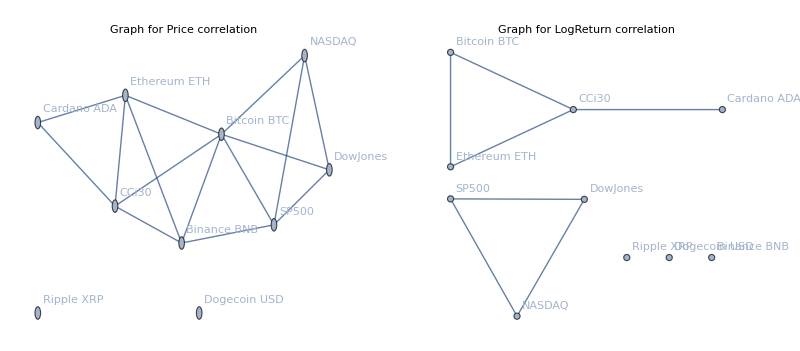

```mathematica
(*Creating and plotting a  weighted adjacent graph for the correlation*)
g=WeightedAdjacencyGraph[alldataNames,
 Round[allCorrelation UnitStep[allCorrelation - .90], .001] /. {1. -> Infinity, 0. -> Infinity}, 
VertexLabels -> "Name",
ImageSize->Large  ,
PlotLabel->"Graph for Price correlation" ] ;

(*Creating and plotting a  weighted adjacent graph for the Returns correlation*)
gL=WeightedAdjacencyGraph[alldataNames,
 Round[logreturnCorrelation UnitStep[logreturnCorrelation - .75], .001] /. {1. -> Infinity, 0. -> Infinity}, 
VertexLabels -> "Name",
ImageSize->Large,
PlotLabel->"Graph for LogReturn correlation"] ;

(*Plotting*)
GraphicsGrid[
{{g,gL}},
ImageSize->Full,Frame->All]
```

Finding closeness centrality and Eigenvector centrality for both correlations:

```mathematica
(*Checking the vertex list and their degree*)
VertexList[g];
VertexDegree[g];
```

```mathematica
(*Finding th e Eigenvector centrality values for all the nodes(price)*)
SortBy[{VertexList[g],EigenvectorCentrality[g]}ᵀ,Last]//Reverse//TableForm
```

Bitcoin BTC | 0.185918
Binance BNB | 0.143945
SP500 | 0.134205
Ethereum ETH | 0.130099
CCi30 | 0.130099
NASDAQ | 0.105597
DowJones | 0.105597
Cardano ADA | 0.0645402
Ripple XRP | 0.
Dogecoin USD | 0.

```mathematica
(*Finding th e Eigenvector centrality values for all the nodes(returns)*)
SortBy[{VertexList[gL],EigenvectorCentrality[gL]}ᵀ,Last]//Reverse//TableForm
```

CCi30 | 0.189269
Ethereum ETH | 0.161757
Bitcoin BTC | 0.161757
SP500 | 0.133333
NASDAQ | 0.133333
DowJones | 0.133333
Cardano ADA | 0.0872174
Ripple XRP | 0.
Dogecoin USD | 0.
Binance BNB | 0.

Plotting the Betweenness Centrality and Community Plot for Both correlations

```mathematica
(*finding the betweeness centrality for price correlation and then plotting it *)
BetweennessCentrality[g];
betweenessPrice=HighlightGraph[g,VertexList[g],
VertexSize->Thread[
VertexList[g]->Rescale[%]]
,PlotLabel->"Betweeness Centrality Plot for Price correlation"];

(*Finding the community plot for the price correlation and seeing if there are any clusters formed*)
communitygraphPrice=HighlightGraph[g,VertexList[g],
VertexSize->Thread[
VertexList[g]->Rescale[BetweennessCentrality[g]]],
PlotLabel->"Community Plot Plot for Price correlation"]//CommunityGraphPlot;
```

```mathematica
(*finding the betweeness centrality for log returns and then plotting it *)
BetweennessCentrality[gL];
betweenesslog=HighlightGraph[g,VertexList[gL],
VertexSize->Thread[
VertexList[gL]->Rescale[%]]
,PlotLabel->"Betweeness Centrality Plot for Log correlation"];

(*Finding the community plot for the Returns and seeing if there are any clusters formed*)
communitygraphlog=HighlightGraph[gL,VertexList[gL],
VertexSize->Thread[
VertexList[gL]->Rescale[BetweennessCentrality[gL]]],
PlotLabel->"Community Plot Plot for Log correlation"]//CommunityGraphPlot;
```

# Plotting Final Graph

```mathematica
(*plotting all four graphs defined on top*)
GraphicsGrid[
{{communitygraphPrice,betweenessPrice},{communitygraphlog,betweenesslog}},
ImageSize->Full,Frame->All]
```

-Graphics-

# Thank you.